```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+NabNabH[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 ν[x] (ψ'[x] (ν[x]^3 σ[x]+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
eqν={ν''[x]==0}
```

{ν''[x]==0}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,X1[xmin]==X1min,X2[xmin]==X2min,X1[xmax]==X1max,X2[xmax]==X2max,ν[xmin]==νmin};
```

```mathematica
σ[x_]:=σc
(*fix the gauge*)
```

```mathematica
eqψ
```

{2 ν[x] (ψ'[x] (σc ν[x]^3+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=-1/2;
ψmax =2.5;
X1min=0;
X2min=0;
X1max=1;
X2max=1;
νmin=1;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,eqν, bcs}],{ψ,X1,X2,ν},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…],ν→InterpolatingFunction[…]}

```mathematica
ν[xmin]/.s
ν[xmax]/.s
```

1.

2.77948

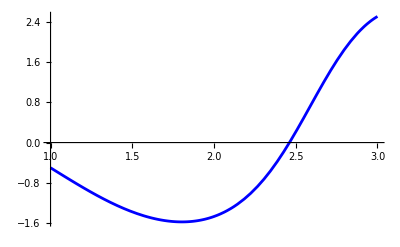

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

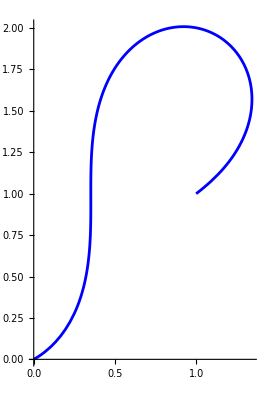

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

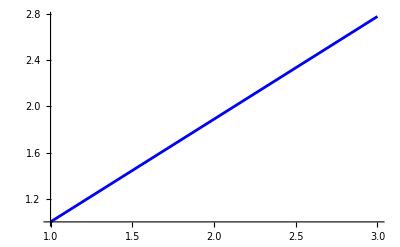

```mathematica
plotνexact=Plot[ν[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,2.38727},{2.8,2.29317},{2.7,2.21046},{2.6,2.1333},{2.5,2.0568},{2.4,1.97676},{2.3,1.88947},{2.2,1.79157},{2.1,1.68002},{2.,1.55221},{1.9,1.40606},{1.8,1.24027},{1.7,1.05463},{1.6,0.850332},{1.5,0.630197},{1.4,0.398803},{1.3,0.162336},{1.2,-0.0717791},{1.1,-0.295388},{1.,-0.5}}

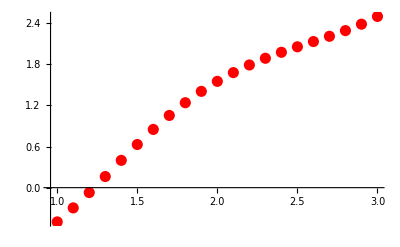

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

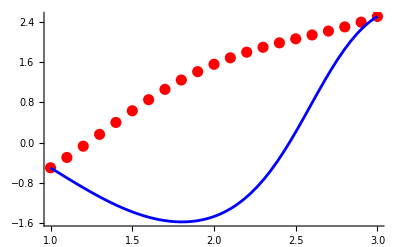

```mathematica
Show[plotψnum,plotψexact,PlotRange->Full]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{1.,1.},{1.19231,1.11385},{1.35998,1.24005},{1.50477,1.37267},{1.62783,1.50759},{1.72948,1.64177},{1.80927,1.7727},{1.86603,1.89801},{1.89794,2.01503},{1.90273,2.12047},{1.87791,2.20999},{1.82108,2.27786},{1.73048,2.31661},{1.60557,2.31697},{1.44758,2.2679},{1.25984,2.15687},{1.04742,1.97008},{0.815847,1.69166},{0.568485,1.3005},{0.302324,0.761227},{3.54336×10^-34,-5.2316×10^-34}}

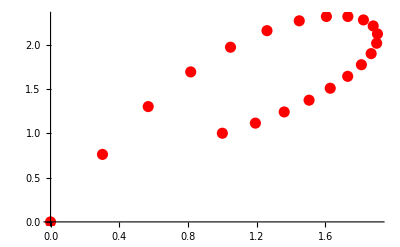

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

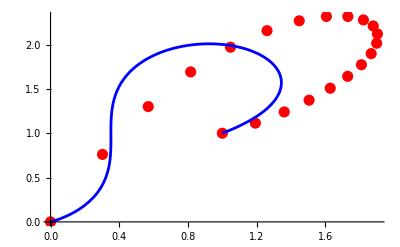

```mathematica
Show[plotXnum,plotXexact,PlotRange->Full]
```

```mathematica
(*check ν*)
```

```mathematica
tν=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/nu.csv"];
tν=Table[{tν[[i,2]],tν[[i,1]]},{i,2,Length[tν]}]
```

{{3.,2.77948},{2.9,2.71831},{2.8,2.65574},{2.7,2.59165},{2.6,2.52594},{2.5,2.45848},{2.4,2.38911},{2.3,2.31766},{2.2,2.24395},{2.1,2.16772},{2.,2.08872},{1.9,2.00661},{1.8,1.92099},{1.7,1.83137},{1.6,1.73714},{1.5,1.63749},{1.4,1.53137},{1.3,1.41733},{1.2,1.29327},{1.1,1.15597},{1.,1.}}

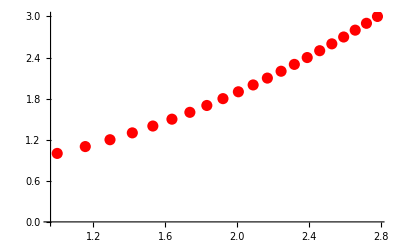

```mathematica
plotνnum=ListPlot[tν,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

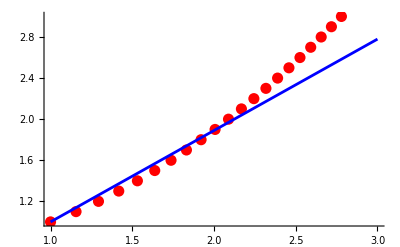

```mathematica
Show[plotνnum,plotνexact,PlotRange->Full]
```